```mathematica
f1 = Table[Piecewise[{{0.5*Sin[4*Pi*(x-0.25)]+0.5,0.25≤x<0.625},{0,0≤x<0.25},{0,0.625≤x≤1}}],{x,0,1, 1/100}]
f2 = Table[Piecewise[{{0.5*Sin[4*Pi*(x-0.625)]+0.5,0.625≤x<1},{0,0≤x<0.625}}] , {x, 0,1,1/100}]
f3 = Table[Piecewise[{{0.5*Sin[4*Pi*(x-0.375)]+0.5,0.25≤x<0.75},{0,0≤x<0.25},{0,0.75≤x≤1}}] +RandomReal[{0,0.1}], {x, 0,1,1/1000}];
f4 = Table[Piecewise[{{0.5*Sin[4*Pi*(x-0.5)]+0.5,0.375≤x<0.875},{0,0≤x<0.25},{0, 0.25≤ x < 0.375},{0,0.875≤x≤1}}] +RandomReal[{0,0.1}], {x, 0,1,1/1000}];
f5 = Table[Piecewise[{{0.5*Sin[4*Pi*(x-0.375)]+0.5,0.25≤x<0.75},{0,0≤x<0.25},{0,0.75≤x≤1}}] +RandomReal[{0,0.1}], {x, 0,1,1/10}];
f6 = Table[Piecewise[{{0.5*Sin[4*Pi*(x-0.5)]+0.5,0.375≤x<0.875},{0,0≤x<0.25},{0, 0.25≤ x < 0.375},{0,0.875≤x≤1}}] +RandomReal[{0,0.1}], {x, 0,1,1/10}];
f7 = Table[Piecewise[{{1,0.25≤x<0.75},{0,0≤x<0.25},{0,0.75≤x≤1}}] +RandomReal[{0,0.1}], {x, 0,1,1/100}];
f8 = Table[Piecewise[{{1,0.375≤x<0.875},{0,0≤x<0.25},{0, 0.25≤ x < 0.375},{0,0.875≤x≤1}}] +RandomReal[{0,0.1}], {x, 0,1,1/100}];
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.5,0.562667,0.624345,0.684062,0.740877,0.793893,0.842274,0.885257,0.922164,0.952414,0.975528,0.991144,0.999013,0.999013,0.991144,0.975528,0.952414,0.922164,0.885257,0.842274,0.793893,0.740877,0.684062,0.624345,0.562667,0.5,0.437333,0.375655,0.315938,0.259123,0.206107,0.157726,0.114743,0.077836,0.0475865,0.0244717,0.00885637,0.000986636,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.531395,0.593691,0.654508,0.71289,0.767913,0.818712,0.864484,0.904508,0.938153,0.964888,0.984292,0.996057,1.,0.996057,0.984292,0.964888,0.938153,0.904508,0.864484,0.818712,0.767913,0.71289,0.654508,0.593691,0.531395,0.468605,0.406309,0.345492,0.28711,0.232087,0.181288,0.135516,0.0954915,0.0618467,0.0351118,0.0157084,0.00394265,0}

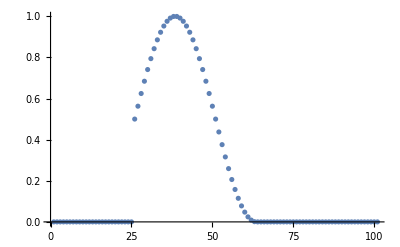

```mathematica
ListPlot[f1]
```

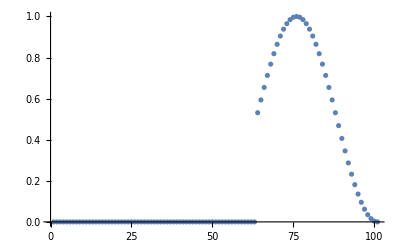

```mathematica
ListPlot[f2]
```

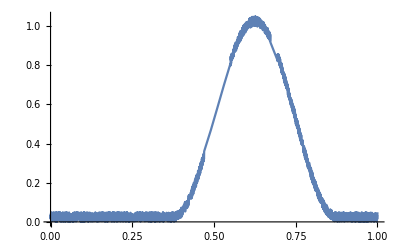

```mathematica
Plot[Piecewise[{{0.5*Sin[4*Pi*(x-0.5)]+0.5,0.375≤x<0.875},{0,0≤x<0.375},{0,0.875≤x≤1}}]+RandomReal[{0,0.05}],{x,0,1}]
```

```mathematica
Export[NotebookDirectory[]<>"plot1.svg",ListPlot[f1]]
Export[NotebookDirectory[]<>"plot2.svg", ListPlot[f2]]
Export[NotebookDirectory[]<>"plot3.svg",ListPlot[f3]]
Export[NotebookDirectory[]<>"plot4.svg", ListPlot[f4]]
Export[NotebookDirectory[]<>"plot7.svg",ListPlot[f7]]
Export[NotebookDirectory[]<>"plot8.svg", ListPlot[f8]]
```

/home/staff/scherping/Build/plot1.svg

/home/staff/scherping/Build/plot2.svg

/home/staff/scherping/Build/plot3.svg

/home/staff/scherping/Build/plot4.svg

/home/staff/scherping/Build/plot7.svg

/home/staff/scherping/Build/plot8.svg

```mathematica
Export[NotebookDirectory[]<>"plot1.csv", f1]
Export[NotebookDirectory[]<>"plot2.csv", f2]
Export[NotebookDirectory[]<>"plot3.csv", f3]
Export[NotebookDirectory[]<>"plot4.csv", f4]
Export[NotebookDirectory[]<>"plot5.csv", f5]
Export[NotebookDirectory[]<>"plot6.csv", f6]
Export[NotebookDirectory[]<>"plot7.csv", f7]
Export[NotebookDirectory[]<>"plot8.csv", f8]
```

/home/staff/scherping/Build/plot1.csv

/home/staff/scherping/Build/plot2.csv

/home/staff/scherping/Build/plot3.csv

/home/staff/scherping/Build/plot4.csv

/home/staff/scherping/Build/plot5.csv

/home/staff/scherping/Build/plot6.csv

/home/staff/scherping/Build/plot7.csv

/home/staff/scherping/Build/plot8.csv